# QHD-vars Different Sets of Dynamical Variables

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

The evolution of the average of an observable A in the Heisenberg representation is given by the equation of motion (EOM): 
 ⅈ ℏ d/dt⟨A⟩=⟨[A,H]⟩
Consider the averages of momentum, position and their products ⟨p⟩, ⟨q⟩, ⟨p^2⟩, ⟨q^2⟩, ⟨pq⟩, ⟨p^3⟩, ⟨p^2 q⟩... The EOMs for the average values are coupled and, in general, form an infinite hierarchy of equations. Quantized Hamilton Dynamics (QHD) terminates this hierarchy by the approximation of the higher order averages via products of the lower order averages. For instance the approximation
⟨ABC⟩≈⟨AB⟩⟨C⟩+⟨AC⟩⟨B⟩+⟨BC⟩⟨A⟩-2⟨A⟩⟨B⟩⟨C⟩
can be used to approximate the third-order averages ⟨q^3⟩ and ⟨pq^2⟩_𝓈 in terms of the first and second order averages ⟨p⟩, ⟨q⟩, ⟨p^2⟩, ⟨q^2⟩ and ⟨p·q⟩_s=⟨(p·q+q·p)/2⟩. Different sets of lower order averages can be used, each set leading to a different QHD approximation. This document shows how to use QUANTUM Mathematica commands to obtain those approximations. QUANTUM is a free Mathematica add-on that can be downloaded from
 http://homepage.cem.itesm.mx/lgomez/quantum/
The calculations in this document are related to the Table 1 of Prezhdo, J. Chem. Phys., Vol 117, No. 7, August 2002, Pages 2995-3002
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDmapeo.pdf .

## Load the Package

First load the Quantum`QHD` package. Write:
Needs["Quantum`QHD`"]
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package and print a welcome message:

```mathematica
Needs["Quantum`QHD`"]
```

Quantum`QHD` 
A Mathematica package for Quantized Hamilton Dynamics approximation to Heisenberg Equations of Motion
by José Luis Gómez-Muñoz
based on the original idea of Kirill Igumenshchev

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.

Execute SetQHDAliases[] in order to use the keyboard to enter QHD objects
SetQHDAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetQHDAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQHDAliases[]
```

ALIASES:
[ESC]on[ESC]     · Quantum concatenation symbol
[ESC]time[ESC]   𝓉 Time symbol
[ESC]hb[ESC]     ℏ Reduced Planck's constant (h bar)
[ESC]ii[ESC]     ⅈ Imaginary I symbol
[ESC]inf[ESC]    ∞ Infinity symbol
[ESC]->[ESC]     → Option (Rule) symbol
[ESC]ave[ESC]    ⟨□⟩ Quantum average template
[ESC]expec[ESC]  ⟨□⟩ Quantum average template
[ESC]symm[ESC]   (□·□)_𝓈 Symmetrized quantum product template
[ESC]comm[ESC]   ⟦□,□⟧_- Commutator template
[ESC]po[ESC]     (□)^□ Power template
[ESC]su[ESC]     □_□ Subscripted variable template
[ESC]posu[ESC]   □_□^□ Power of a subscripted variable template
[ESC]fra[ESC]    □/□ Fraction template
[ESC]eva[ESC]    □/.{□→□,□→□} Evaluation (ReplaceAll) template

SetQHDAliases[] must be executed again in each new notebook that is created, only one time per notebook.

## Commutation Relationships and Hamiltonian

In order to enter the templates and symbols ⟦□,□⟧_-, □/□, ℏ and ⅈ you can either use the QHD palette (toolbar) or press the keys [ESC]comm[ESC], [ESC]fra[ESC], [ESC]hb[ESC] and [ESC]ii[ESC]. The Hamiltonian that will be used in the rest of this document is stored in the variable th below:

```mathematica
Clear[a,p,q];
SetQuantumObject[q,p];
⟦q,p⟧_-=ⅈ*ℏ;
th=p^2/2+q^2/(2!)+q^3/(3!)+q^4/(4!)
```

p^2/2+q^2/2+q^3/6+q^4/24

## Different QHD approximations to the Heisenberg Equations of Motion

Using only {⟨p⟩,⟨q⟩} as QHD dynamical variables (see the introduction of this document) we obtain classical dynamics equations. The command QHDHierarchy takes as its first argument the list of dynamical variables, the second argument is the variable which is used to start the hierarchy, and the third argument is the Hamiltonian. The resulting hierarchy is stored in the variable hpq below:

```mathematica
hpq=QHDHierarchy[{p,q},q,th]
```

{{QHDLabel,Dynamical variables: {⟨p⟩,⟨q⟩}},{⟨q⟩,⟨p⟩},{⟨p⟩,-⟨q⟩-⟨q⟩^2/2-⟨q⟩^3/6}}

The command QHDForm gives a nice, tabular representation of the hierarchy:

```mathematica
QHDForm[hpq]
```

Dynamical variables: {⟨p⟩,⟨q⟩}
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨p⟩)/d𝓉=-⟨q⟩-⟨q⟩^2/2-⟨q⟩^3/6

Using {⟨p⟩,⟨q⟩,⟨q^2⟩} as QHD dynamical variables it is allowed to give an initial value to ⟨q^2⟩ (average of the square) that is different from the initial value of ⟨q⟩^2 (square of the average), which actually happens in quantum wavepackets. Compare the two equations above with the three equations below:

```mathematica
hpqq2=QHDHierarchy[{p,q,q^2},q,th];
QHDForm[hpqq2]
```

Dynamical variables: {⟨p⟩,⟨q⟩,⟨q^2⟩}
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨p⟩)/d𝓉=-⟨q⟩+⟨q⟩^3/3-⟨q^2⟩/2-1/2 ⟨q⟩ ⟨q^2⟩
(d⟨q^2⟩)/d𝓉=2 ⟨p⟩ ⟨q⟩

The standard Mathematica command TeXForm can be used in the output of QHDForm in order to generate a TEX version of the hierarchy for LATEX editors:

```mathematica
TeXForm[QHDForm[hpqq2]]
```

\begin{array}{|l|}
\hline
 \text{Dynamical variables: }\left\{\langle
   p\rangle ,\langle q\rangle ,\left\langle
   q^2\right\rangle \right\} \\
\hline
 \frac{d\langle q\rangle
   }{d\mathit{t}}=\langle p\rangle  \\
\hline
 \frac{d\langle p\rangle
   }{d\mathit{t}}=-\langle q\rangle
   +\frac{\langle q\rangle
   ^3}{3}-\frac{\left\langle
   q^2\right\rangle }{2}-\frac{1}{2}
   \langle q\rangle  \left\langle
   q^2\right\rangle  \\
\hline
 \frac{d\left\langle q^2\right\rangle
   }{d\mathit{t}}=2 \langle p\rangle 
   \langle q\rangle  \\
\hline
\end{array}

We can export the hierarchy to a TEX file, as shown below:

```mathematica
Export["hierarchy.tex",QHDForm[hpqq2]]
```

hierarchy.tex

See the content of the file below:

```mathematica
FilePrint["hierarchy.tex"]
```

%% AMS-LaTeX Created by Wolfram Mathematica 8.0 : www.wolfram.com

\documentclass{article}
\usepackage{amsmath, amssymb, graphics, setspace}

\newcommand{\mathsym}[1]{{}}
\newcommand{\unicode}[1]{{}}

\newcounter{mathematicapage}
\begin{document}

\[\begin{array}{|l|}
\hline
 \text{Dynamical variables: }\left\{\langle p\rangle ,\langle q\rangle ,\left\langle q^2\right\rangle \right\} \\
\hline
 \frac{d\langle q\rangle }{d\mathit{t}}=\langle p\rangle  \\
\hline
 \frac{d\langle p\rangle }{d\mathit{t}}=-\langle q\rangle +\frac{\langle q\rangle ^3}{3}-\frac{\left\langle q^2\right\rangle }{2}-\frac{1}{2} \langle
q\rangle  \left\langle q^2\right\rangle  \\
\hline
 \frac{d\left\langle q^2\right\rangle }{d\mathit{t}}=2 \langle p\rangle  \langle q\rangle  \\
\hline
\end{array}\]

\end{document}

QHDDifferentialEquations transforms the hierarchy to standard Mathematica notation for differential equations, therefore those equations could be part of the input for Mathematica commands like NDSolve, DSolve, etc. The symbol for time 𝓉 can be entered pressing the keys [ESC]time[ESC], see the equations below:

```mathematica
QHDDifferentialEquations[hpqq2]
```

{⟨q⟩'[𝓉]==⟨p⟩[𝓉],⟨p⟩'[𝓉]==-⟨q⟩[𝓉]+1/3 (⟨q⟩[𝓉])^3-1/2 ⟨q^2⟩[𝓉]-1/2 ⟨q⟩[𝓉] ⟨q^2⟩[𝓉],⟨q^2⟩'[𝓉]==2 ⟨p⟩[𝓉] ⟨q⟩[𝓉]}

A different symbol for time can be specified. The operator → can be entered pressing the keys [ESC][MINUS][GREATERTHAN][ESC], see the equations below:

```mathematica
QHDDifferentialEquations[hpqq2,QHDSymbolForTime->z]
```

{⟨q⟩'[z]==⟨p⟩[z],⟨p⟩'[z]==-⟨q⟩[z]+1/3 (⟨q⟩[z])^3-1/2 ⟨q^2⟩[z]-1/2 ⟨q⟩[z] ⟨q^2⟩[z],⟨q^2⟩'[z]==2 ⟨p⟩[z] ⟨q⟩[z]}

The command QHDGraphPlot shows the relationship between the dynamical variables, each arrow points from a first dynamical variable to a second variable that includes the first one in its equation of motion, see the graph below:

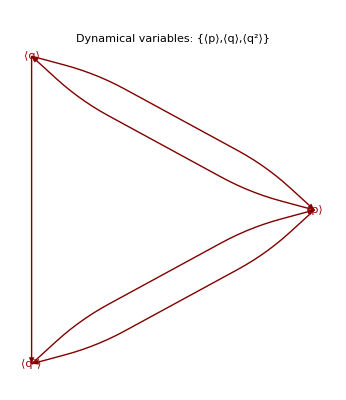

```mathematica
QHDGraphPlot[hpqq2]
```

Here we use all the first and second order variables to build the hierarchy, see the table below:

```mathematica
hsec=QHDHierarchy[{p,q,q^2,p^2,p·q},q,th];
QHDForm[hsec]
```

Dynamical variables: {⟨p⟩,⟨q⟩,⟨q^2⟩,⟨p^2⟩,⟨pq⟩_𝓈}
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨p⟩)/d𝓉=-⟨q⟩+⟨q⟩^3/3-⟨q^2⟩/2-1/2 ⟨q⟩ ⟨q^2⟩
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩+⟨q⟩^3+⟨q⟩^4/3-⟨q^2⟩-3/2 ⟨q⟩ ⟨q^2⟩-(⟨q^2⟩^2)/2
(d⟨p^2⟩)/d𝓉=2 ⟨p⟩ ⟨q⟩^2+2/3 ⟨p⟩ ⟨q⟩^3-⟨p⟩ ⟨q^2⟩-2 ⟨pq⟩_𝓈-2 ⟨q⟩ ⟨pq⟩_𝓈-⟨q^2⟩ ⟨pq⟩_𝓈

We can generate the same hierarchy using a number 2 as the first argument of QHDHierarchy, compare the table above and the table below:

```mathematica
h2=QHDHierarchy[2,q,th];
QHDForm[h2]
```

Closure procedure was applied to order 2
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨p⟩)/d𝓉=-⟨q⟩+⟨q⟩^3/3-⟨q^2⟩/2-1/2 ⟨q⟩ ⟨q^2⟩
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩+⟨q⟩^3+⟨q⟩^4/3-⟨q^2⟩-3/2 ⟨q⟩ ⟨q^2⟩-(⟨q^2⟩^2)/2
(d⟨p^2⟩)/d𝓉=2 ⟨p⟩ ⟨q⟩^2+2/3 ⟨p⟩ ⟨q⟩^3-⟨p⟩ ⟨q^2⟩-2 ⟨pq⟩_𝓈-2 ⟨q⟩ ⟨pq⟩_𝓈-⟨q^2⟩ ⟨pq⟩_𝓈

The command QHDGraphPlot shows the relationship between the dynamical variables, each arrow points from a first dynamical variable to a second variable that includes the first one in its equation of motion, compare the table above with the graph below:

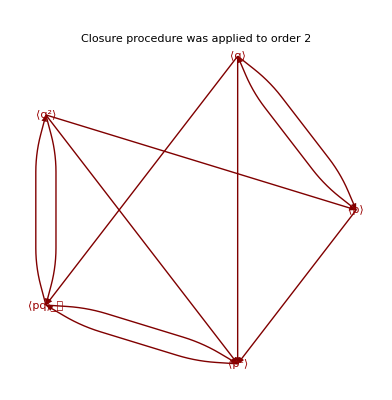

```mathematica
QHDGraphPlot[h2]
```

Here we use all the first and second order variables and ⟨q^3⟩ as dynamical variables

```mathematica
hsecq3=QHDHierarchy[{p,q,q^2,p^2,p·q,q^3},q,th];
QHDForm[hsecq3]
```

Dynamical variables: {⟨p⟩,⟨q⟩,⟨q^2⟩,⟨p^2⟩,⟨pq⟩_𝓈,⟨q^3⟩}
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨p⟩)/d𝓉=-⟨q⟩-⟨q^2⟩/2-⟨q^3⟩/6
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨q^3⟩)/d𝓉=-6 ⟨p⟩ ⟨q⟩^2+3 ⟨p⟩ ⟨q^2⟩+6 ⟨q⟩ ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩-⟨q⟩^4-⟨q^2⟩+2 ⟨q⟩^2 ⟨q^2⟩-(⟨q^2⟩^2)/2-⟨q^3⟩/2-2/3 ⟨q⟩ ⟨q^3⟩
(d⟨p^2⟩)/d𝓉=2 ⟨p⟩ ⟨q⟩^2-⟨p⟩ ⟨q^2⟩+⟨p⟩ ⟨q⟩ ⟨q^2⟩-1/3 ⟨p⟩ ⟨q^3⟩-2 ⟨pq⟩_𝓈-2 ⟨q⟩ ⟨pq⟩_𝓈-⟨q^2⟩ ⟨pq⟩_𝓈

The command QHDGraphPlot shows the relationship between the dynamical variables, each arrow points from a first dynamical variable to a second variable that includes the first one in its equation of motion, compare the table above with the graph below:

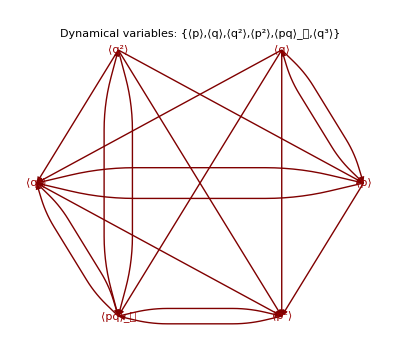

```mathematica
QHDGraphPlot[hsecq3]
```

Here we calculate the hierarchy using all the third order variables. This calculation takes several seconds in a laptop computer, notice the ℏ terms in the equation at the bottom of the table below:

```mathematica
h3=QHDHierarchy[3,q,th];
QHDForm[h3]
```

Closure procedure was applied to order 3
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨p⟩)/d𝓉=-⟨q⟩-⟨q^2⟩/2-⟨q^3⟩/6
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨q^3⟩)/d𝓉=3 ⟨p q^2⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩-⟨q⟩^4-⟨q^2⟩+2 ⟨q⟩^2 ⟨q^2⟩-(⟨q^2⟩^2)/2-⟨q^3⟩/2-2/3 ⟨q⟩ ⟨q^3⟩
(d⟨p q^2⟩_𝓈)/d𝓉=-3 ⟨q⟩^4-⟨q⟩^5+6 ⟨q⟩^2 ⟨q^2⟩-(3 ⟨q^2⟩^2)/2+5/2 ⟨q⟩ ⟨q^2⟩^2-⟨q^3⟩-2 ⟨q⟩ ⟨q^3⟩-5/3 ⟨q^2⟩ ⟨q^3⟩+2 ⟨p^2 q⟩_𝓈
(d⟨p^2⟩)/d𝓉=-2 ⟨p⟩ ⟨q⟩^3+2 ⟨p⟩ ⟨q⟩ ⟨q^2⟩-1/3 ⟨p⟩ ⟨q^3⟩-2 ⟨pq⟩_𝓈+2 ⟨q⟩^2 ⟨pq⟩_𝓈-⟨q^2⟩ ⟨pq⟩_𝓈-⟨p q^2⟩_𝓈-⟨q⟩ ⟨p q^2⟩_𝓈
(d⟨p^2 q⟩_𝓈)/d𝓉=⟨p^3⟩-6 ⟨p⟩ ⟨q⟩^3-2 ⟨p⟩ ⟨q⟩^4+6 ⟨p⟩ ⟨q⟩ ⟨q^2⟩+⟨p⟩ ⟨q^2⟩^2-⟨p⟩ ⟨q^3⟩+6 ⟨q⟩^2 ⟨pq⟩_𝓈-3 ⟨q^2⟩ ⟨pq⟩_𝓈+4 ⟨q⟩ ⟨q^2⟩ ⟨pq⟩_𝓈-4/3 ⟨q^3⟩ ⟨pq⟩_𝓈-2 ⟨p q^2⟩_𝓈-3 ⟨q⟩ ⟨p q^2⟩_𝓈-2 ⟨q^2⟩ ⟨p q^2⟩_𝓈
(d⟨p^3⟩)/d𝓉=ℏ^2/4+1/4 ℏ^2 ⟨q⟩-9 ⟨p⟩^2 ⟨q⟩^2+3 ⟨p^2⟩ ⟨q⟩^2-3 ⟨p⟩^2 ⟨q⟩^3+3 ⟨p⟩^2 ⟨q^2⟩-3/2 ⟨p^2⟩ ⟨q^2⟩+3/2 ⟨p^2⟩ ⟨q⟩ ⟨q^2⟩-1/2 ⟨p^2⟩ ⟨q^3⟩+12 ⟨p⟩ ⟨q⟩ ⟨pq⟩_𝓈+3 ⟨p⟩ ⟨q^2⟩ ⟨pq⟩_𝓈-3 ⟨pq⟩_𝓈^2+3 ⟨q⟩ ⟨pq⟩_𝓈^2-3 ⟨p^2 q⟩_𝓈-3 ⟨q⟩ ⟨p^2 q⟩_𝓈-3/2 ⟨q^2⟩ ⟨p^2 q⟩_𝓈-3 ⟨p⟩ ⟨p q^2⟩_𝓈-3 ⟨pq⟩_𝓈 ⟨p q^2⟩_𝓈

The command QHDGraphPlot shows the relationship between the dynamical variables, each arrow points from a first dynamical variable to a second variable that includes the first one in its equation of motion, compare the table above with the graph below:

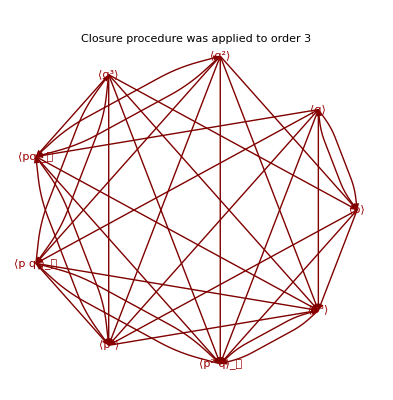

```mathematica
QHDGraphPlot[h3]
```

QUANTUM is a free Mathematica add-on that can be downloaded from
 http://homepage.cem.itesm.mx/lgomez/quantum/
The calculations in this document are related to the Table 1 of Prezhdo, J. Chem. Phys., Vol 117, No. 7, August 2002, Pages 2995-3002
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDmapeo.pdf .

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx